```mathematica
rules={{0, 1, 0}->2,{0, 2, 0}->3, {0, 3, 0}->4, {0, 4, 0}->5, {0, 5, 0}->1, {5, 0, 0}->6, {6, 0, 0}->6};
k=1+Max[Max[Values[rules]], Max[Max/@Keys[rules]]]
rules1=ConstantArray[0, k^3];
Do[With[{key=First[rr], v=Last[rr]},rules1[[FromDigits[key, k]]]=v], {rr, rules}];
rules1
Length[rules1]
rules2=FromDigits[Reverse[rules1], k]
```

7

{0,0,0,0,0,0,2,0,0,0,0,0,0,3,0,0,0,0,0,0,4,0,0,0,0,0,0,5,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

343

246534086507316101966903820624015963098881319413194412130874773475245762834830173877712398421331097681397848238702499970883314824630108083062619492916605937398239665005594212530724418532807453419351315413263849421391533420060567369028186188964869935

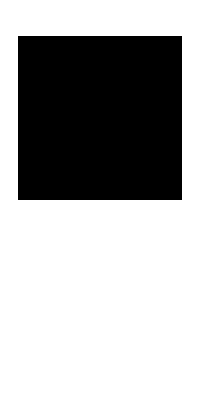

```mathematica
ArrayPlot[CellularAutomaton[{, k}, {{1}, 0}, 1]]
```